5.1 Make a list of the first 10 squares, in reverse order.

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

5.2 Find the total for the first 10 squares.

```mathematica
Total[Range[10]^2]
```

385

5.3 Make a plot of the first 10 squares starting at 1.

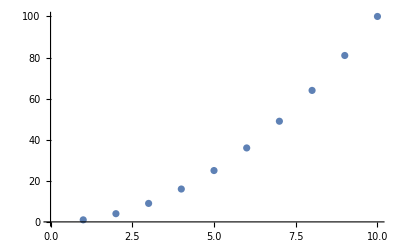

```mathematica
ListPlot[Range[10]^2]
```

5.4 Use Sort, Join and Range to create {1, 1, 2, 2, 3, 3, 4, 4}.

```mathematica
Sort[Join[Range[4], Range[4]]]
```

{1,1,2,2,3,3,4,4}

5.5 Use Range and + to make a list of numbers from 10 to 20, inclusive.

```mathematica
Range[11]+9
```

{10,11,12,13,14,15,16,17,18,19,20}

5.6 Make a combined list of the first 5 squares and cubes, sorted into order.

```mathematica
Sort[Join[Range[5]^2, Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

5.7 Find the number of digits in 2^128.

```mathematica
Length[IntegerDigits[2^128]]
```

39

5.8 Find the first digit of 2^32.

```mathematica
First[IntegerDigits[2^32]]
```

4

5.9 Find the first 10 digits in 2^100.

```mathematica
Take[IntegerDigits[2^100], 10]
```

{1,2,6,7,6,5,0,6,0,0}

5.10 Find the largest digit that appears in 2^20.

```mathematica
Max[IntegerDigits[2^20]]
```

8

5.11 Find how many zeros appear in the digital of 2^1000.

```mathematica
Count[IntegerDigits[2^1000], 0]
```

28

5.12 Use Part, Sort and IntegerDigits to find the second-smallest digit in 2^20.

```mathematica
Part[Sort[IntegerDigits[2^20]], 2]
```

1

5.13 Make a line plot of the sequence of digits that appear in 2^128.

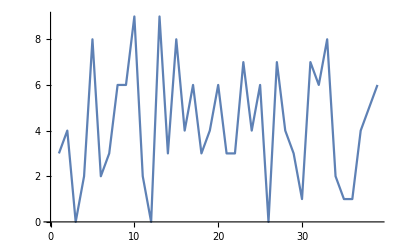

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

5.14 Use Take and Drop to get the sequence 11 through 20 from Range[100].

```mathematica
Take[Drop[Range[100], 10], 10]
```

{11,12,13,14,15,16,17,18,19,20}